Coherent state

```mathematica
ϕ[n_,α_]:=ⅇ^(-Abs[α]^2/2)α^n/(√(n!));
```

A useful function of gain

```mathematica
G[g_]:=(√(g^2-1))/g;
```

Unnormalized state

```mathematica
PsiTilde[n_,α_,g_]:=ⅇ^(-Abs[G[g]α]^2/2)(1/g^2-n G[g]^2)ⅇ^(-Abs[α/g]^2/2)(α/g)^n/(√(n!));
```

```mathematica
Solve[1/g^2==n G[g]^2,n]
```

{{n→1/(-1+g^2)}}

Appropriate value of gain for the condition of zero overlap of ACS with the attenuated coherent state

```mathematica
g0[α_]:=1/(√(1-1/Abs[α]^2));
```

```mathematica
g1[α_]:=√((2-Abs[α]^2+√(Abs[α]^4+4))/2);
```

Squared Denominator of the final state

```mathematica
NormACS[α_,g_]:=(1/g^2-G[g]^2 Abs[α/g]^2)^2+G[g]^4 Abs[α/g]^2;
```

Probability of success (P_s)

```mathematica
Manipulate[Plot[ⅇ^(-Abs[G[g]α]^2)NormACS[α,g],{g,1,1.6},GridLines->{{{g0[α],Black},{g1[α],Black},{g/.NSolve[Simplify[D[ⅇ^(-Abs[G[g]α]^2)NormACS[α,g],g]]==0&&g>1&&Element[g,Reals],g][[2]],Black}},{.025,.05,.075,.1}},PlotRange->Full,AxesOrigin->{1,0},AxesLabel->{"g","P_s"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black}],{α,2,3,1}]
```

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

ReplaceAll::reps: {g} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

ReplaceAll::reps: {g} is neither a list of replacement rules nor a valid dispatch table, and so cannot be used for replacing.

General::stop: Further output of ReplaceAll::reps will be suppressed during this calculation.

NSolve::nsmet: This system cannot be solved with the methods available to NSolve.

General::stop: Further output of NSolve::nsmet will be suppressed during this calculation.

```mathematica
InnerProductPACS[α_,g_]:=((α/g)/(√(Abs[α/g]^2+1))(1/g^2-G[g]^2(Abs[α/g]^2+1)))/(√NormACS[α,g]);
InnerProductDFS[α_,g_]:=-(G[g]^2 α/g)/(√NormACS[α,g]);
InnerProductCS[α_,g_]:=(1/g^2-Abs[α/g]^2 G[g]^2)/(√NormACS[α,g]);
C0g1[α_]:=FullSimplify[InnerProductCS[α,g1[α]]];
C1g1[α_]:=FullSimplify[InnerProductDFS[α,g1[α]]];
```

```mathematica
C0g1[x]
```

(2+Abs[x]^4+√(4+Abs[x]^4)-x (1+√(4+Abs[x]^4)) Conjugate[x])/(√(-2 Abs[x]^6+2 (2+√(4+Abs[x]^4)) (2+Abs[x]^4-2 x Conjugate[x])))

Fidelity of the final state with DFS, CS and PACS as a function of gain

```mathematica
Manipulate[Plot[{(InnerProductDFS[α,ⅇ^(x^4)])^2,(InnerProductCS[α,ⅇ^(x^4)])^2,(InnerProductPACS[α,ⅇ^(x^4)])^2},{x,0.35,1.2},GridLines->{{{Log[g0[α]]^(1/4),Black},{Log[g1[α]]^(1/4),Black}},None},AxesOrigin->{0.35,0},PlotRange->Full,PlotStyle->{{Dotted,Thick,Red},Black,{Blue,Dashed}},AxesLabel->{"(ln (g))^(1/4)","Fidelity"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black},PlotLegends->{"Displaced Number State","Coherent State","Photon-Added Coherent State"}],{α,1.01,7}]
```

```mathematica
Manipulate[Plot[(InnerProductPACS[α,x])^2,{x,1,1.01},AxesOrigin->{1,0},PlotRange->Full,PlotStyle->{Black},AxesLabel->{"g","Fidelity"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black},PlotLegends->{"Photon-Added Coherent State"}],{α,3,10,1}]
```

Normalized state

```mathematica
ψ[n_,α_,g_]:=((1/g^2-n G[g]^2)ⅇ^(-Abs[α/g]^2/2)(α/g)^n/(√(n!)))/(√NormACS[α,g]);
```

Checking that the total probability adds up to 1

```mathematica
∑_(n=0)^∞ N[ψ[n,√10,g0[√10]]]^2
```

1.

Coefficients of Coherent and Photon-Added part in the final state

```mathematica
CoefficientOfCoherentState[α_,g_]:=(1/g^2)/(√NormACS[α,g]);
CoefficientOfPhotonAddedState[α_,g_]:=-(α/g G[g]^2 √(Abs[α/g]^2+1))/(√NormACS[α,g]);
```

```mathematica
Manipulate[Plot[{CoefficientOfCoherentState[α,ⅇ^(x^4)],CoefficientOfPhotonAddedState[α,ⅇ^(x^4)]},{x,0,1.2},GridLines->{{{Log[g0[α]]^(1/4),Black},{Log[g1[α]]^(1/4),Black}},None},AxesOrigin->{0,0},PlotRange->Full,PlotStyle->{Gray,Black},AxesLabel->{"(ln (g))^(1/4)","C"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black},PlotLegends->{"Coefficient of Coherent State","Coefficient of Photon-Added Coherent State"}],{α,1.01,7}]
```

Plot of attenuated coherent state and corresponding ACS for different values of average photon number for the original (unattenuated) coherent state

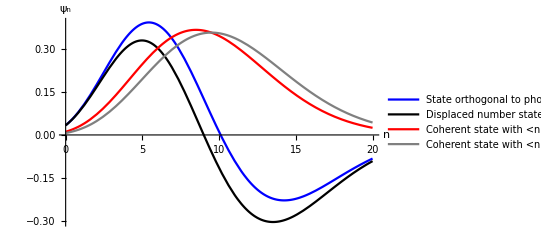

```mathematica
navg0=10;
Plot[{ψ[n,√navg0,g1[√navg0]],ψ[n,√navg0,g0[√navg0]],ϕ[n,(√navg0)/g0[√navg0]],ϕ[n,√navg0]},{n,0,2navg0},PlotRange->Full,PlotStyle->{Blue,Black,Red,Gray},AxesLabel->{"n","ψ_n"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black},PlotLegends->{"State orthogonal to photon added state (when g=g_1)","Displaced number state with <n>=10 (when g=g_0)","Coherent state with <n>=9","Coherent state with <n>=10"}]
```

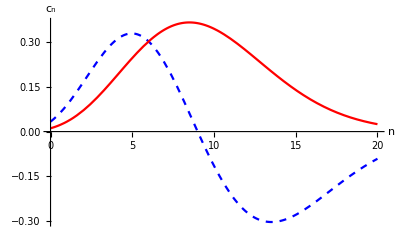

```mathematica
cn=Plot[{ψ[n,√navg0,g0[√navg0]],ϕ[n,(√navg0)/g0[√navg0]]},{n,0,2navg0},PlotRange->Full,PlotStyle->{{Blue,Dashed},Red},AxesLabel->{"n","c_n"},LabelStyle->{FontSize->20,FontFamily->"Times", ,Black}]
(*Export["cn.pdf", cn,ImageResolution-> 1000]*)
```

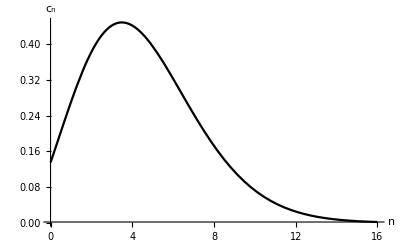

```mathematica
cng[α_,g_]:=Plot[{ψ[n,α,g]},{n,0,4 Abs[α]^2},PlotRange->Full,PlotStyle->{{Black},Red},AxesLabel->{"n","c_n"},LabelStyle->{FontSize->16,FontFamily->"Times", ,Black}]
cng[2,1]
```

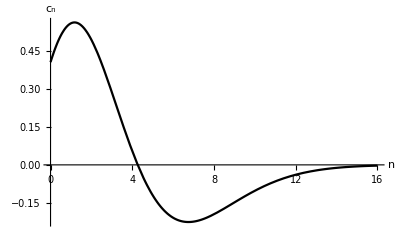

```mathematica
cng[2,1.111]
```

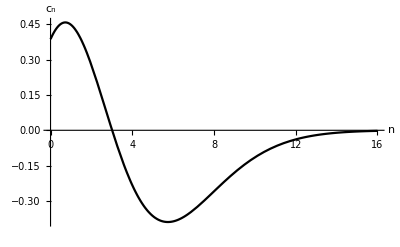

```mathematica
cng[2,1.154]
```

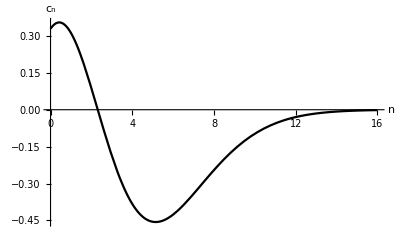

```mathematica
cng[2,1.197]
```

Average photon number

```mathematica
C1[α_,g_]:=InnerProductDFS[α,g];
C0[α_,g_]:=InnerProductCS[α,g];
AveragePhotonNumber[α_,g_]:=Abs[C0[α,g]]^2 Abs[α/g]^2+Abs[C1[α,g]]^2 (Abs[α/g]^2+1)-((2 Abs[α]^2 G[g]^2) (1-Abs[α]^2 G[g]^2))/(g^4 NormACS[α,g]);
Manipulate[Plot[AveragePhotonNumber[α,ⅇ^(x^4)],{x,0,1.2},GridLines->{{{Log[g0[α]]^(1/4),{Thick,Red}},{Log[g1[α]]^(1/4),{Dashed,Black,Thick}}},{{Abs[α]^2,{Red}},Abs[α/g1[α]]^2}},AxesOrigin->{0,0},PlotRange->Full,PlotStyle->{Gray,Black},AxesLabel->{"(ln (g)\!\(\*SuperscriptBox[\()\), \(1/4\)]\)","<n>"},LabelStyle->{FontSize->14,FontFamily->"Times",Null,Black}],{α,1.01,4}]
```

```mathematica
Manipulate[Plot[(x/((x^2-1)β))^2,{x,1.01,2},AxesOrigin->{1.01,0},PlotRange->Full,PlotStyle->{Gray,Black},AxesLabel->{"g","|α|^2"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black}],{β,1.01,4}]
```

Variance of photon number

```mathematica
AverageOfPhotonNumberSquared[α_,g_]:=Abs[C0[α,g]]^2(Abs[α/g]^2+Abs[α/g]^4)+Abs[C1[α,g]]^2(3 Abs[α/g]^2+(Abs[α/g]^2+1)^2)-(2 Abs[α]^2 G[g]^2)/(g^4 NormACS[α,g])(1-Abs[α]^2 G[g]^2)(2 Abs[α/g]^2+1);
VarianceOfPhotonNumber[α_,g_]:=AverageOfPhotonNumberSquared[α,g]-AveragePhotonNumber[α,g]^2;
```

```mathematica
Manipulate[Plot[VarianceOfPhotonNumber[α,ⅇ^(x^4)],{x,0.2,1.25},GridLines->{{{Log[g0[α]]^(1/4),Red},{Log[g1[α]]^(1/4),Black}},{{3 Abs[α/g0[α]]^2,Red}}},AxesOrigin->{0.2,0},PlotRange->Full,PlotStyle->{Gray,Black},AxesLabel->{"(ln (g))^(1/4)","y"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black}],{α,2,√6}]
```

Average and Variance of photon number plotted together

```mathematica
Manipulate[Plot[{AveragePhotonNumber[α,ⅇ^(x^4)],VarianceOfPhotonNumber[α,ⅇ^(x^4)]},{x,.2,2},GridLines->{{{Log[g0[α]]^(1/4),Purple},{Log[g1[α]]^(1/4),Black}},{{3 Abs[α/g0[α]]^2,Blue},{Abs[α]^2,Red},Abs[α/g1[α]]^2}},AxesOrigin->{.2,0},PlotRange->Full,PlotStyle->{Blue,Black},AxesLabel->{"(ln (g))^(1/4)","Var(n)"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black},PlotLegends->{"Average photon number","Variance of photon number"}],{α,1.01,4}]
```

Mandel’s Q parameter

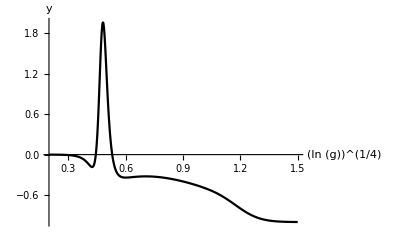

```mathematica
α=3;
Plot[VarianceOfPhotonNumber[α,ⅇ^(x^4)]/AveragePhotonNumber[α,ⅇ^(x^4)]-1,{x,.2,1.5},GridLines->{{{Log[g0[α]]^(1/4),Purple},{Log[g1[α]]^(1/4),Black},{Log[g]^(1/4)/.NSolve[Simplify[D[ⅇ^(-Abs[G[g]α]^2)NormACS[α,g],g]]==0&&g>1&&Element[g,Reals],g][[2]],Green}},{{3 Abs[α/g0[α]]^2,Blue},{Abs[α]^2,Red},Abs[α/g1[α]]^2}},AxesOrigin->{.2,0},PlotRange->Full,PlotStyle->{Blue,Black},AxesLabel->{"(ln (g))^(1/4)","y"},LabelStyle->{FontSize->14,FontFamily->"Times", ,Black}]
```

Number state representations

```mathematica
PhotonAdded[α_,n_]:=(ⅇ^(-Abs[α]^2/2))/(α √(Abs[α]^2+1))n α^n/(√(n!));
DisplacedOnePhoton[α_,n_]:=ⅇ^(-Abs[α]^2/2)((n/α -α*)/(√(n!)))α^n;
InnerProductBetweenPhotonAddedAndDisplaced[α_]:=∑_(n=0)^∞ (PhotonAdded[α,n])* DisplacedOnePhoton[α,n];
Manipulate[Plot[{PhotonAdded[α,n],DisplacedOnePhoton[α,n]},{n,1,15},PlotRange->Full],{α,0.001,2.5}]
```

```mathematica
(*Plot[InnerProductBetweenPhotonAddedAndDisplaced[α],{α,0.1,3}]*)
```

```mathematica
(*Plot[InnerProductBetweenPhotonAddedAndDisplaced[α],{α,3,4}]*)
```

```mathematica
(*Plot[InnerProductBetweenPhotonAddedAndDisplaced[α],{α,4,5}]*)
```

```mathematica
(*InnerProductBetweenCoherentAndPhotonAdded[α_]:=1/(α √(Abs[α]^2+1))∑_(n=0)^∞ n(ϕ[n,α])*ϕ[n,α];
Plot[InnerProductBetweenCoherentAndPhotonAdded[α],{α,0.1,3}]*)
```

```mathematica
(*ContourPlot[Qfunction[x, y, 1.195, 2, 0], {x, -0.4, 4.4}, {y, -2.4, 2.4}, GridLines -> Automatic, GridLinesStyle -> Black, Axes -> True, AxesLabel -> {"Re(α)", "Im(α)"}, ImageSize -> Scaled[1], AxesStyle -> {Thick, Thick}, 
  LabelStyle -> {FontSize -> 25, FontFamily -> "Times", Null, Black}, PlotLabel -> Style["(d)", FontFamily -> "Times", FontSize -> 25]]
ContourPlot[Qfunction[x, y, 1.19, 2, 0], {x, -0.4, 4.4}, {y, -2.4, 2.4}, GridLines -> Automatic, GridLinesStyle -> Black, Axes -> True, AxesLabel -> {"Re(α)", "Im(α)"}, ImageSize -> Scaled[1], AxesStyle -> {Thick, Thick}, 
  LabelStyle -> {FontSize -> 25, FontFamily -> "Times", Null, Black}, PlotLabel -> Style["(d)", FontFamily -> "Times", FontSize -> 25]]*)
```

Q functions

```mathematica
Qfunction[x_,y_,g_,R_,ϕ_]:=1/π Abs[(C0[R ⅇ^(ⅈ ϕ),g]+C1[R ⅇ^(ⅈ ϕ),g]((x-ⅈ y)-(R ⅇ^(ⅈ ϕ))/g))ⅇ^(-1/2(Abs[x+ⅈ y]^2+(R/g)^2-2(x-ⅈ y)R/g ⅇ^(ⅈ ϕ)))]^2
```

```mathematica
p1=ContourPlot[Qfunction[x,y,1,2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,.3}}],ColorFunctionScaling->False,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->45,FontFamily->"Times",,Black},PlotLabel-> Style["(a)",FontFamily->"Times",FontSize->45],PlotLegends->BarLegend[{Automatic,{0,0.3}},5,"LabelingFunction"->(Round[#3[[1]],.01]&)],PlotPoints->50,ImageSize->Scaled[1],Contours->5,ImagePadding->All];
p2=ContourPlot[Qfunction[x,y,g1[2],2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,.2}}],ColorFunctionScaling->False,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->45,FontFamily->"Times",,Black},PlotLabel-> Style["(b)",FontFamily->"Times",FontSize->45],PlotLegends->BarLegend[{Automatic,{0,0.2}},5,"LabelingFunction"->(Round[#3[[1]],.01]&)],PlotPoints->50,ImageSize->Scaled[1],Contours->5,ImagePadding->All];
p3=ContourPlot[Qfunction[x,y,g0[2],2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,.1}}],ColorFunctionScaling->False,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->45,FontFamily->"Times",,Black},PlotLabel-> Style["(c)",FontFamily->"Times",FontSize->45],PlotLegends->BarLegend[{Automatic,{0,0.1}},5,"LabelingFunction"->(Round[#3[[1]],.01]&)],PlotPoints->50,ImageSize->Scaled[1],Contours->5,ImagePadding->All];
p4=ContourPlot[Qfunction[x,y,1.195,2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,.2}}],ColorFunctionScaling->False,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->45,FontFamily->"Times",,Black},PlotLabel-> Style["(d)",FontFamily->"Times",FontSize->45],PlotLegends->BarLegend[{Automatic,{0,0.2}},5,"LabelingFunction"->(Round[#3[[1]],.01]&)],PlotPoints->50,ImageSize->Scaled[1],Contours->5,ImagePadding->All];

(*LabelStyle->{FontSize->20,FontFamily->"Times",Black},
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontFamily->"Times",FontSize->18}],Right]*)
```

```mathematica
(*pm1=ContourPlot[Qfunction[x,y,1,2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->45,FontFamily->"Times",,Black},PlotLabel-> Style["(a)",FontFamily->"Times",FontSize->45],PlotLegends->Automatic,PlotPoints->55,ImageSize->Scaled[1],Contours->5];
pm2=ContourPlot[Qfunction[x,y,g1[2],2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->45,FontFamily->"Times",,Black},PlotLabel-> Style["(b)",FontFamily->"Times",FontSize->45],PlotLegends->Automatic,PlotPoints->55,ImageSize->Scaled[1],Contours->5];
pm3=ContourPlot[Qfunction[x,y,g0[2],2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->45,FontFamily->"Times",,Black},PlotLabel-> Style["(c)",FontFamily->"Times",FontSize->45],PlotLegends->Automatic,PlotPoints->55,ImageSize->Scaled[1],Contours->5];
pm4=ContourPlot[Qfunction[x,y,1.195,2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->45,FontFamily->"Times",,Black},PlotLabel-> Style["(d)",FontFamily->"Times",FontSize->45],PlotLegends->Automatic,PlotPoints->55,ImageSize->Scaled[1],Contours->5];*)

(*LabelStyle->{FontSize->20,FontFamily->"Times",Black},
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontFamily->"Times",FontSize->18}],Right]*)
```

```mathematica
(*Export["5.pdf",p1]
Export["5b.pdf",p2]
Export["5c.pdf",p3]
Export["5d.pdf",p4]*)
```

```mathematica
GraphicsColumn[{p1,p2,p3,p4},ImageSize->Scaled[1]]
```

```mathematica
(*pn1=ContourPlot[Qfunction[x,y,1,2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,.31}}],ColorFunctionScaling->False,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->40,FontFamily->"Times",,Black},PlotLabel-> Style["(a)",FontFamily->"Times",FontSize->40],PlotPoints->50,ImageSize->Scaled[1]];
pn2=ContourPlot[Qfunction[x,y,g1[2],2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,.31}}],ColorFunctionScaling->False,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->40,FontFamily->"Times",,Black},PlotLabel-> Style["(b)",FontFamily->"Times",FontSize->40],PlotPoints->50,ImageSize->Scaled[1]];
pn3=ContourPlot[Qfunction[x,y,g0[2],2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,.31}}],ColorFunctionScaling->False,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->40,FontFamily->"Times",,Black},PlotLabel-> Style["(c)",FontFamily->"Times",FontSize->40],PlotPoints->50,ImageSize->Scaled[1]];
pn4=ContourPlot[Qfunction[x,y,1.195,2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,.31}}],ColorFunctionScaling->False,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->40,FontFamily->"Times",,Black},PlotLabel-> Style["(d)",FontFamily->"Times",FontSize->40],PlotPoints->50,ImageSize->Scaled[1]];*)
```

```mathematica
(*pd1=DensityPlot[Qfunction[x,y,1,2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,1/π}}],ColorFunctionScaling->False,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->40,FontFamily->"Times",,Black},PlotLabel-> Style["(a)",FontFamily->"Times",FontSize->40],PlotLegends->BarLegend[{Automatic,{0,1/π}}],PlotPoints->50,ImageSize->Scaled[1]];
pd2=DensityPlot[Qfunction[x,y,g1[2],2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,1/π}}],ColorFunctionScaling->False,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->40,FontFamily->"Times",,Black},PlotLabel-> Style["(b)",FontFamily->"Times",FontSize->40],PlotLegends->BarLegend[{Automatic,{0,1/π}}],PlotPoints->50,ImageSize->Scaled[1]];
pd3=DensityPlot[Qfunction[x,y,g0[2],2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,1/π}}],ColorFunctionScaling->False,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->40,FontFamily->"Times",,Black},PlotLabel-> Style["(c)",FontFamily->"Times",FontSize->40],PlotLegends->BarLegend[{Automatic,{0,1/π}}],PlotPoints->50,ImageSize->Scaled[1]];
pd4=DensityPlot[Qfunction[x,y,1.195,2,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,ColorFunction->ColorData[{"M10DefaultDensityGradient",{0,1/π}}],ColorFunctionScaling->False,PlotRange->Full,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->40,FontFamily->"Times",,Black},PlotLabel-> Style["(d)",FontFamily->"Times",FontSize->40],PlotLegends->BarLegend[{Automatic,{0,1/π}}],PlotPoints->50,ImageSize->Scaled[1]];*)

(*DensityPlot[Qfunction[x,y,1,2,0],{x,-0.4,4.4},{y,-2.4,2.4},Axes->True,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->25,FontFamily->"Times",,Black},PlotLabel-> Style["(a)",FontFamily->"Times",FontSize->25],PlotLegends->Placed[BarLegend[{Automatic,{0,1/π}}],Right]]
PlotLegends->Placed[BarLegend[Automatic,LabelStyle->{FontFamily->"Times",FontSize->18}],Right]*)
```

```mathematica
(*graphics = Legended[GraphicsColumn[{pn1,pn2,pn3,pn4}],Placed[BarLegend[{"M10DefaultDensityGradient",{0,1/π}},LegendLayout->"Row",LabelStyle->{FontSize->40,FontFamily->"Times",,Black}, LegendMarkerSize->300],Bottom]]*)
```

```mathematica
(*Export["graphics.pdf", graphics]*
```

graphics.pdf

```mathematica
(*pl= Import[Export["pl.pdf",GraphicsColumn[{p1,p2,p3,p4}],ImageResolution-> 1000,"AllowRasterization"-> False]]
Export["testplt.emf",pl[[1]],ImageResolution-> 1000]*)
```

```mathematica
(*pll = GraphicsColumn[{p1, p2, p3, p4}];
Export["pll.emf", pll, ImageSize -> Scaled[1],"AllowRasterization" -> False];*)
```

Plots for the paper

```mathematica
(*α=2;
plt1=Plot[AveragePhotonNumber[α,ⅇ^(x^4)],{x,0.2,1.25},GridLines->{{{Log[g0[α]]^(1/4),{Red}},{Log[g1[α]]^(1/4),{Dashed,Black}}},None},GridLinesStyle->Opacity[1],AxesOrigin->{0.2,0},PlotRange->Full,PlotStyle->{Gray,Black}, AxesLabel->{"(ln (g))^(1/4)",AngleBracket[n]},LabelStyle->{FontSize->20,FontFamily->"Times", Black}]
plt2=Plot[VarianceOfPhotonNumber[α,ⅇ^(x^4)],{x,0.2,1.25},GridLines->{{{Log[g0[α]]^(1/4),Red},{Log[g1[α]]^(1/4),{Dashed,Black}}},None},GridLinesStyle->Opacity[1],AxesOrigin->{0.2,0},PlotRange->Full,PlotStyle->{Gray,Black},AxesLabel->{"(ln (g))^(1/4)","Var(StyleBox[\"n\",FontSlant->\"Italic\"])"},LabelStyle->{FontSize->20,FontFamily->"Times", Black}]
plt3=Plot[{(InnerProductDFS[α,ⅇ^(x^4)])^2,(InnerProductCS[α,ⅇ^(x^4)])^2,(InnerProductPACS[α,ⅇ^(x^4)])^2},{x,0.35,1.2},GridLines->{{{Log[g0[α]]^(1/4),Black},{Log[g1[α]]^(1/4),Black}},None},GridLinesStyle->Opacity[0.8], AxesOrigin->{0.35,0},PlotRange->Full,PlotStyle->{{Dotted,Thick,Red},Black,{Blue,Dashed}},AxesLabel->{"(ln g)^(1/4)","Fidelity"},LabelStyle->{FontSize->20,FontFamily->"Times",Black}]
plt4=Plot[(InnerProductPACS[10,x])^2,{x,1,1.009},AxesOrigin->{1,0},PlotRange->Full,AxesLabel->{"g","Fidelity"},PlotStyle-> Black,LabelStyle->{FontSize->20,FontFamily->"Times",Black}]*)
```

```mathematica
(*pl1= Import[Export["plt1.pdf",plt1,ImageSize->Scaled[1],ImageResolution-> 1000,"AllowRasterization"-> False]];
Export["plt11.emf",pl1[[1]],ImageResolution-> 1000]
pl2= Import[Export["plt2.pdf",plt2,ImageSize->Scaled[1],ImageResolution-> 1000,"AllowRasterization"-> False]];
Export["plt21.emf",pl2[[1]],ImageResolution-> 1000]
pl3= Import[Export["plt3.pdf",plt3,ImageSize->Scaled[1],ImageResolution->1000, "AllowRasterization"-> False]];
Export["plt313.emf",pl3[[1]],ImageResolution-> 1000, "AllowRasterization"-> False]
p4= Import[Export["plt4.pdf",plt4,ImageSize->Scaled[1],ImageResolution-> 2500,"AllowRasterization"-> False]];
Export["plt41.emf",p4[[1]],ImageSize->Scaled[1],ImageResolution-> 2500,"AllowRasterization" -> False]*)
```

```mathematica
(*aasf =p4[[1]]*)
```

```mathematica
(*Export["testaasf.emf",aasf,ImageSize-> Scaled[1],ImageResolution-> 2500,"AllowRasterization" -> False]*)
```

```mathematica
(*Export["plt3.svg",plt3,ImageSize->Scaled[1],ImageResolution->2500, "AllowRasterization"-> False]*)
```

Plot Animations

```mathematica
(*qfunc[α_,g_]:=ContourPlot[Qfunction[x,y,g,α,0],{x,-0.4,4.4},{y,-2.4,2.4},
GridLines->Automatic,GridLinesStyle->Black,Axes->True,AxesLabel->{"Re(α)","Im(α)"},AxesStyle->{Thick,Thick},LabelStyle->{FontSize->12,FontFamily->"Times",,Black}];
number[α_,g_]:=Plot[{ψ[n,α,g],ϕ[n,α/g]},{n,0,2 α^2},PlotRange->0.58,PlotStyle->{{Blue,Dashed},Red},AxesLabel->{"n","c_n"},LabelStyle->{FontSize->12,FontFamily->"Times", ,Black},PlotLegends->Placed[{Style[#,12]&/@{"|ψ⟩","|α/g⟩"}},Below],ImageSize->Scaled[1]];
avg[α_,g_]:=Plot[AveragePhotonNumber[α,ⅇ^(x^4)],{x,0,1.2},GridLines->{{{Log[g]^(1/4),Red}},None},GridLinesStyle->Opacity[1],AxesOrigin->{0,0},PlotRange->Full,PlotStyle->{Gray,Black}, AxesLabel->{"(ln (g))^(1/4)",AngleBracket[n]},LabelStyle->{FontSize->12,FontFamily->"Times", Black}];
var[α_,g_]:=Plot[VarianceOfPhotonNumber[α,ⅇ^(x^4)],{x,0,1.2},GridLines->{{{Log[g]^(1/4),Red}},None},GridLinesStyle->Opacity[1],AxesOrigin->{0,0},PlotRange->Full,PlotStyle->{Gray,Black}, AxesLabel->{"(ln (g))^(1/4)","Var(n)"},LabelStyle->{FontSize->12,FontFamily->"Times", Black}];
fidelity[α_,g_]:=Plot[{(InnerProductDFS[α,ⅇ^(x^4)])^2,(InnerProductCS[α,ⅇ^(x^4)])^2,(InnerProductPACS[α,ⅇ^(x^4)])^2},{x,0,1.2},GridLines->{{{Log[g]^(1/4),Red}},None},GridLinesStyle->Opacity[1],AxesOrigin->{0,0},PlotRange->Full,PlotStyle->{{Dotted,Thick,Red},Black,{Blue,Dashed}},AxesLabel->{"(ln (g))^(1/4)","Fidelity"},LabelStyle->{FontSize->10,FontFamily->"Times", Black},PlotLegends->Placed[{Style[#,10]&/@{"Displaced Number State","Coherent State","Photon-Added Coherent State"}},Below],ImageSize->Scaled[1]]
m=Manipulate[GraphicsGrid[{{qfunc[2,g],number[2,g],},{fidelity[2,g],avg[2,g],var[2,g]}},ImageSize->Scaled[0.8]],{g,1,1.197,Appearance-> "Open"}]*)
```

```mathematica
(*Export["m1.gif", m, "AnimationRepetitions" -> Infinity]*)
```

Detector dark counts

```mathematica
nc[α_,g_]:=√(Abs[c0u[α,g]]^2+Abs[c1u[α,g]]^2);
c0u[α_,g_]:=(α*)/g;
c1u[α_,g_]:=1;
c0[α_,g_]:=c0u[α,g]/nc[α,g];
c1[α_,g_]:=c1u[α,g]/nc[α,g];
(*FidBasic[p_,α_,g_]:=p^2 Abs[C0[α,g]]^2 + (1-p )^2+p(1-p)Abs[C0[α,g]]^2+p(1-p)Abs[(c0[α,g])*C0[α,g]+(c1[α,g])*C1[α,g]]^2;
Manipulate[Plot[FidBasic[p,α,1.111],{p,0,1},AxesLabel->{"Dark count prb","Fidelity"},PlotRange->{0,1}],{α,0,10}]*)
```

```mathematica
(*Manipulate[Plot3D[FidBasic[p,α,g],{p,0,1},{g,0,10},AxesLabel->{"Dark count prb","g","Fidelity"},PlotRange->{0,1}],{α,0,10}]*)
```

```mathematica
(*Plot[{G[g],G[g]^2,G[g]^3},{g,1,3},PlotLegends->Automatic]*)
```

```mathematica
d0u[α_,g_]:=((α*)/g)^2;
d1u[α_,g_]:=2(α*)/g;
d2u[α_,g_]:=√2; 
nd[α_,g_]:=√(Abs[d0u[α,g]]^2+Abs[d1u[α,g]]^2+Abs[d2u[α,g]]^2);
d0[α_,g_]:=d0u[α,g]/nd[α,g];
d1[α_,g_]:=d1u[α,g]/nd[α,g];
d2[α_,g_]:=d2u[α,g]/nd[α,g];
```

```mathematica
e0u[α_,g_]:=-((α*)/g)1/g+(G[g]Abs[α/g])^2/2 α*;
e1u[α_,g_]:=(-1+(G[g]Abs[α])^2)/g;
e2u[α_,g_]:=G[g]^2 α/(√2);
ne[α_,g_]:=√(Abs[e0u[α,g]]^2+Abs[e1u[α,g]]^2+Abs[e2u[α,g]]^2);
e0[α_,g_]:=e0u[α,g]/ne[α,g];
e1[α_,g_]:=e1u[α,g]/ne[α,g];
e2[α_,g_]:=e2u[α,g]/ne[α,g];
```

```mathematica
FidTwo[d_,e_,α_,g_]:=d^2 Abs[C0[α,g]]^2+d(1-d-e)Abs[(c0[α,g])*C0[α,g]+(c1[α,g])*C1[α,g]]^2+d e Abs[(d0[α,g])*C0[α,g]+(d1[α,g])*C1[α,g]]^2+(1-d)d Abs[C0[α,g]]^2+(1-d-e)(1-d) +(1-d)e Abs[(e0[α,g])*C0[α,g]+(e1[α,g])*C1[α,g]]^2; 
FidApprox[d_,e_,α_,g_]:=d^2 Abs[C0[α,g]]^2+d(1-d-e)Abs[(c0[α,g])*C0[α,g]+(c1[α,g])*C1[α,g]]^2+(1-d)d Abs[C0[α,g]]^2+(1-d-e)(1-d)  ;
```

```mathematica
Manipulate[Manipulate[Plot3D[{FidTwo[d,e,α,g],FidApprox[d,e,α,g]},{e,0,1-d},{g,1.001,1.2},AxesLabel->{"e","g","Fidelity"},PlotRange->{0,1},PlotStyle->Opacity[0.5]],{d,0,.9999999}],{α,0,10}]
```

```mathematica
(*e=0.1;
eplt1=Plot[{FidBasic[d,2,1.154],FidApprox[d,e,2,1.154],FidTwo[d,e,2,1.154]},{d,0,1-e},PlotLegends->{"Only d","Lower bound","d and l"},PlotStyle->{{Thick,Blue},{Thick,Black},{Thick,Red}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotLabel->"l=0.1",AxesLabel->{"Pr⟦Dark Count|Detector signal⟧","Fidelity"}]
e=0.2;
eplt2=Plot[{FidBasic[d,2,1.154],FidApprox[d,e,2,1.154],FidTwo[d,e,2,1.154]},{d,0,1-e},PlotLegends->{"Only d","Lower bound","d and l"},PlotStyle->{{Thick, Blue},{Thick,Black},{Thick,Red}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotLabel->"l=0.2",AxesLabel->{"Pr⟦Dark Count|Detector signal⟧","Fidelity"}]
e=0.5;
eplt5=Plot[{FidBasic[d,2,1.154],FidApprox[d,e,2,1.154],FidTwo[d,e,2,1.154]},{d,0,1-e},PlotLegends->{"Only d","Lower bound","d and l"},PlotStyle->{{Thick, Blue},{Thick,Black},{Thick,Red}},LabelStyle->{FontSize->16,FontFamily->"Times",Black},PlotLabel->"l=0.5",AxesLabel->{"Pr⟦Dark Count|Detector signal⟧","Fidelity"}]*)
```

```mathematica
(*l=0.1;
lplt1=Plot[{FidBasic[d,2,1.154],FidApprox[d,l,2,1.154],FidTwo[d,l,2,1.154]},{d,0,1-l},PlotStyle->{{Thick,Dashed,Blue},{Thick,DotDashed,Red},{Thick,Black}},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotLabel->"(a)",AxesLabel->{"d","Fidelity"},ImageSize->Scaled[1]];
l=0.2;
lplt2=Plot[{FidBasic[d,2,1.154],FidApprox[d,l,2,1.154],FidTwo[d,l,2,1.154]},{d,0,1-l},PlotStyle->{{Thick, Dashed ,Blue},{Thick,DotDashed,Red},{Thick,Black}},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotLabel->"(b)",AxesLabel->{"d","Fidelity"},ImageSize->Scaled[1]];
l=0.5;
lplt5=Plot[{FidBasic[d,2,1.154],FidApprox[d,l,2,1.154],FidTwo[d,l,2,1.154]},{d,0,1-l},PlotStyle->{{Thick, Dashed,Blue},{Thick,DotDashed,Red},{Thick,Black}},LabelStyle->{FontSize->20,FontFamily->"Times",Black},PlotLabel->"(c)",AxesLabel->{"d","Fidelity"},ImageSize->Scaled[1]];
plotFidel2=GraphicsColumn[{lplt1,lplt2,lplt5}]
Export["plotF.emf",plotFidel2,ImageSize-> Scaled[1],ImageResolution->1000]*)
```

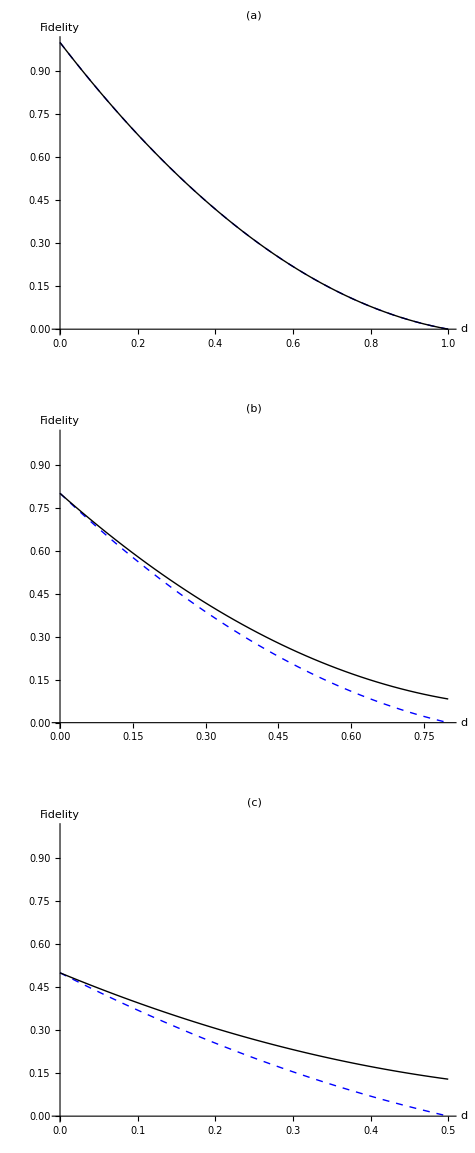

```mathematica
l=0;
lplt1=Plot[{FidApprox[d,l,2,1.154],FidTwo[d,l,2,1.154]},{d,0,1-l},PlotStyle->{{Thick,Dashed,Blue},{Thick,Black}},LabelStyle->{FontSize->30,FontFamily->"Times",Black},PlotLabel->"(a)",LabelStyle->{FontSize->20,FontFamily->"Times",Black},AxesLabel->{"d","Fidelity"},ImageSize->Scaled[1],PlotRange->{0,1}];
l=0.2;
lplt2=Plot[{FidApprox[d,l,2,1.154],FidTwo[d,l,2,1.154]},{d,0,1-l},PlotStyle->{{Thick,Dashed,Blue},{Thick,Black}},LabelStyle->{FontSize->30,FontFamily->"Times",Black},PlotLabel->"(b)",LabelStyle->{FontSize->20,FontFamily->"Times",Black},AxesLabel->{"d","Fidelity"},ImageSize->Scaled[1],PlotRange->{0,1}];
l=0.5;
lplt5=Plot[{FidApprox[d,l,2,1.154],FidTwo[d,l,2,1.154]},{d,0,1-l},PlotStyle->{{Thick,Dashed,Blue},{Thick,Black}},LabelStyle->{FontSize->30,FontFamily->"Times",Black},PlotLabel->"(c)",LabelStyle->{FontSize->20,FontFamily->"Times",Black},AxesLabel->{"d","Fidelity"},ImageSize->Scaled[1],PlotRange->{0,1}];
plotFidel2=GraphicsColumn[{lplt1,lplt2,lplt5}]
```

```mathematica
(*Export["Fidel.pdf",plotFidel2]*)
(*Export["plt1.pdf",plt1]
Export["plt2.pdf",plt2]
Export["plt3.pdf",plt3]
Export["plt4.pdf",plt4]*)
```